```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\GitHub\optics_R_exp\optics_data

```mathematica
r0=0.1
```

0.1

```mathematica
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
```

```mathematica
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data=Transpose[{x1,y1}];
data1=data⟦;;⟧;
```

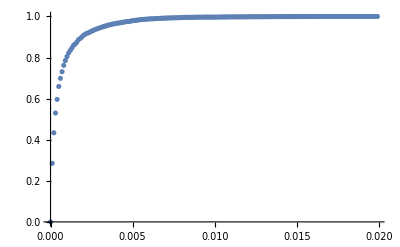

```mathematica
p1=ListPlot[data,PlotRange->All]
```

```mathematica
r0=0.2
```

0.2

```mathematica
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
```

```mathematica
ExpandFileName["R_0.2.csv"]
```

C:\Users\user\Documents\GitHub\optics_R_exp\optics_data\R_0.2.csv

```mathematica
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data2=Transpose[{x1,y1}];
data21=data2⟦;;⟧;
```

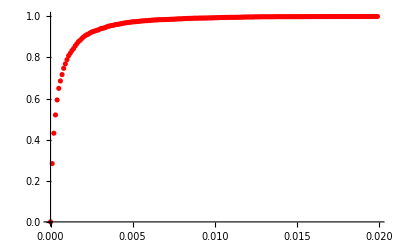

```mathematica
p2=ListPlot[data2,PlotRange->All,PlotStyle->Red]
```

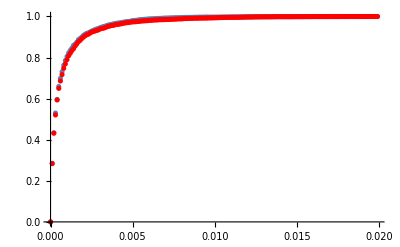

```mathematica
Show[p1,p2]
```

```mathematica
r0=0.3
```

0.3

```mathematica
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
```

```mathematica
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data3=Transpose[{x1,y1}];
data31=data3⟦;;⟧;
```

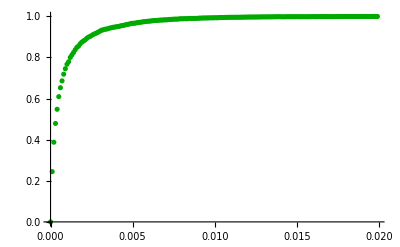

```mathematica
p3=ListPlot[data3,PlotRange->All,PlotStyle->Darker[Green]]
```

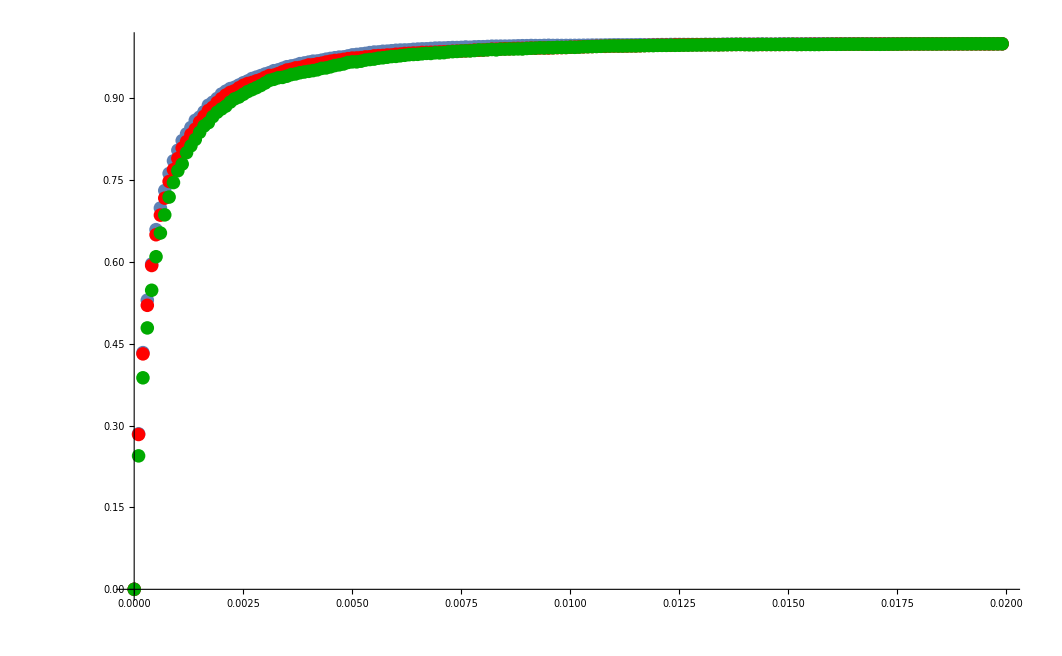

```mathematica
Show[p1,p2,p3]
```

```mathematica
r0=0.4
```

0.4

```mathematica
gridfilename=StringJoin["grid_",ToString[r0],".csv"];
rfilename=StringJoin["R_",ToString[r0],".csv"];
```

```mathematica
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data4=Transpose[{x1,y1}];
data41=data4⟦;;⟧;
```

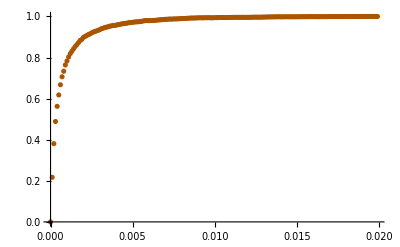

```mathematica
p4=ListPlot[data4,PlotRange->All,PlotStyle->Darker[Orange]]
```

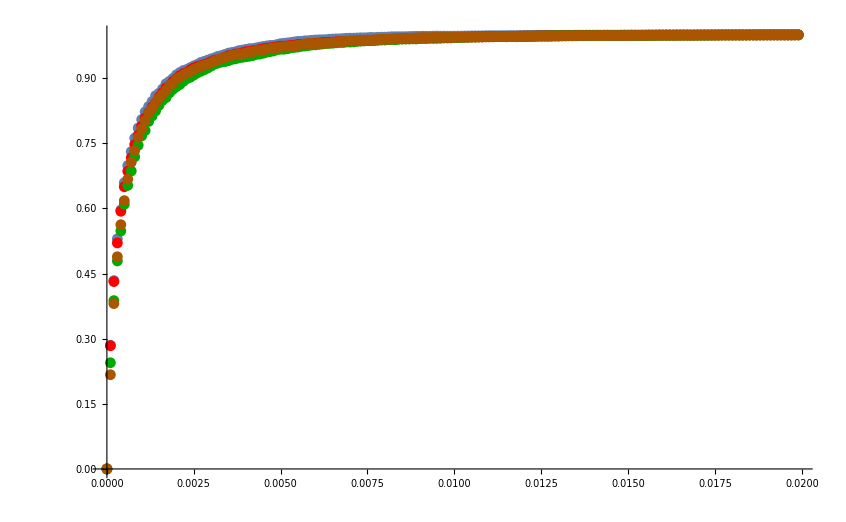

```mathematica
Show[p1,p2,p3,p4]
```

```mathematica
Length[data]
```

200

```mathematica
Length[data2]
```

200

```mathematica
Length[data3]
```

200

```mathematica
Length[data4]
```

200